```mathematica
Predicting Bitcoin Bubbles
```

## References

- Transaction Dynamics of Blockchain and Predictable Bitcoin Bubbles. - https://polybox.ethz.ch/index.php/s/LzLmTZXzqF8rCAs

- Are Bitcoin Bubbles Predictable? Combining a Generalized Metcalfe’s Law and the LPPLS Model. - https://arxiv.org/pdf/1803.05663.pdf

- Metcalfe's law.

## Resources

- Bitcoin hourly price: Recent (≥ 2024) data - bitstamp.com.

- Bitcoin circulating supply: https://www.blockchain.com/charts/total-bitcoins.

## In This Notebook

LPPLS model implementation (2026 ed.).

```mathematica
base=DirectoryName[NotebookFileName[]];
lastPriceDate=DateString[Yesterday,"ISODate"]
```

2026-01-23

```mathematica
hourlyPricesUrl="https://www.cryptodatadownload.com/cdd/Bitstamp_BTCUSD_1h.csv";
prices =Import[hourlyPricesUrl, HeaderLines->1]
```

```mathematica
(* First price date: *)
firstDownloadedDateTime=prices[[-1]][[2]];
{firstDownloadedDate,firstDownloadedTime}=StringSplit[firstDownloadedDateTime];
firstPriceDate=firstDownloadedDate
```

2018-05-15

```mathematica
(* Some freshness checks: *)
lastDownloadedDateTime=prices[[2]][[2]];
{lastDownloadedDate, lastDownloadedTime}=StringSplit[lastDownloadedDateTime]
{DateString[DatePlus[lastDownloadedDate, -1], "ISODate"]==lastPriceDate, lastDownloadedTime=="00:00:00"}
```

{2026-01-24,00:00:00}

{True,True}

```mathematica
closingPrices={#[[1]],#[[7]]}&/@prices
```

```mathematica
(* Filter non-numerical values *)
closingPricesFilter=Select[closingPrices, NumberQ[#[[2]]]&]
```

```mathematica
(* Hourly data *)
hourlyPrices=SortBy[closingPricesFilter, First]
```

```mathematica
Length[hourlyPrices]
```

67439

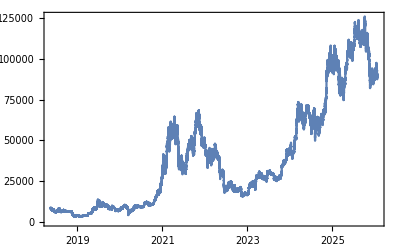

```mathematica
DateListPlot[hourlyPrices,DateFunction:> (FromUnixTime[#]&)]
```

```mathematica
Export[base<>"csv/Bitcoin_price-hourly-"<>StringDelete[firstPriceDate, "-"]<>"-"<>StringDelete[lastPriceDate, "-"]<>".csv",hourlyPrices]
```

/Users/mauro/Projects/Bitcoin/csv/Bitcoin_price-hourly-20180515-20260123.csv

```mathematica
(* Convert to market capitalization, using circulating supply data, from blockchain.info *)
(* Load circulating supply data: https://www.blockchain.com/charts/total-bitcoins *)
supplyJsonData = Import["https://api.blockchain.info/charts/total-bitcoins?timespan=all&sampled=true&metadata=false&daysAverageString=1d&cors=true&format=json"];
```

```mathematica
supplyJson=supplyJsonData[[6]][[2]]
```

```mathematica
supplyTs=supplyJson[[All, 1]][[All,2]];
supplyQuantity=supplyJson[[All, 2]][[All,2]];
```

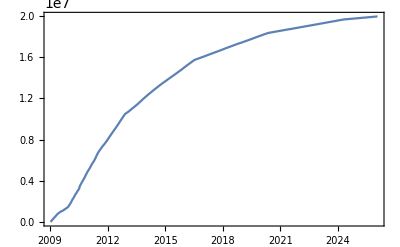

```mathematica
supplyTimestamps=MapThread[{#1, #2}&,{supplyTs, supplyQuantity}];
DateListPlot[supplyTimestamps,DateFunction:> (FromUnixTime[#]&)]
```

```mathematica
(* Create an interpolating function from it *)
supplyFunction=Block[{},Off[ InterpolatingFunction::dmval];Interpolation[supplyTimestamps]]
```

InterpolatingFunction[…]

```mathematica
{supplyTimestamps[[1]][[1]], supplyTimestamps[[-1]][[1]]}
```

{1231568277,1768875044}

```mathematica
{hourlyPrices[[1]][[1]],hourlyPrices[[-1]][[1]]}
```

{1526364000,1769212800}

```mathematica
{supplyFunction[hourlyPrices[[1]][[1]]], supplyFunction[hourlyPrices[[-3]][[1]]]}
```

{1.70341×10^7,1.99798×10^7}

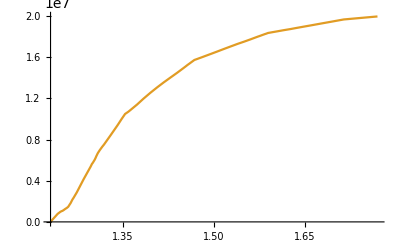

```mathematica
Plot[{,supplyFunction[i]}, {i, supplyTimestamps[[1]][[1]], supplyTimestamps[[-1]][[1]]}]
```

```mathematica
(* Generate hourly market capitalization data *)
hourlyMarketCap={#[[1]], #[[2]]*supplyFunction[#[[1]]]}&/@hourlyPrices
```

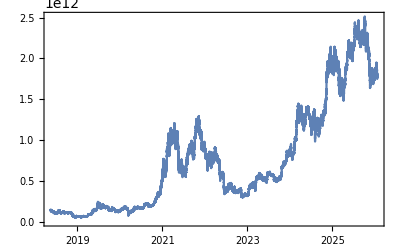

```mathematica
DateListPlot[hourlyMarketCap, DateFunction:> (FromUnixTime[#]&)]
```

```mathematica
(* Use the Log Market Cap *)
logMarketCap= {#[[1]], Log[#[[2]]]}&/@hourlyMarketCap
```

```mathematica
(* Appendix 5.1. Example: Analyze / predict the 2026 bubble turning point: *)
(* Generalized to multiple bubbles *)
bubblesDate={{"2025-11-23", lastPriceDate}}
```

{{2025-11-23,2026-01-23}}

```mathematica
bubbleN=Length[bubblesDate]
```

1

```mathematica
(* Timestamp indexes: *)
bubblesTimestampIndex={UnixTime[#[[1]]], UnixTime[#[[2]]]}&/@bubblesDate
```

{{1763852400,1769122800}}

```mathematica
bubblesDays=(#[[2]]-#[[1]])/86400&/@bubblesTimestampIndex
```

{61}

```mathematica
bubbles=Table[Select[logMarketCap,bubblesTimestampIndex[[i]][[1]]≤#[[1]]≤ bubblesTimestampIndex[[i]][[2]]&], {i, bubbleN}];
#[[1]]&/@bubbles
```

{{1763852400,28.1555}}

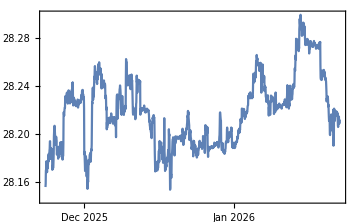

```mathematica
DateListPlot[bubbles, ImageSize->Medium, DateFunction->(FromUnixTime[#]&)]
```

```mathematica
(* Scale data horizontally and vertically *)
scaleH[data_]:= Module[{peaks, first},
(* Scale bubbles horizontally (0-1) (set 1 at the true peaks) *)
peaks=MaximalBy[data, Last][[1]];
first = data[[1]];
{(#[[1]]-first[[1]])/(peaks[[1]]-first[[1]]),#[[2]]}&/@data
]
```

```mathematica
scaleV[data_]:= Module[{min, max},
(* Rescale vertically *)
min=Min[Last /@data];
max=Max[Last /@data];
{#[[1]],(#[[2]]-min)/(max-min)}&/@data
]
```

```mathematica
bubblesScaled=scaleV[scaleH[#]]&/@ bubbles//N;
#[[-1]]&/@bubblesScaled
```

{{1.15366,0.4011}}

```mathematica
Length/@bubblesScaled
```

{1465}

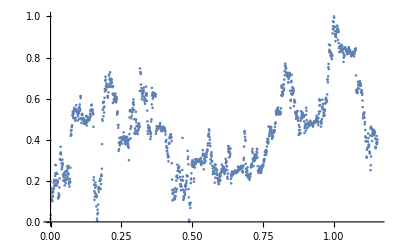

```mathematica
(* LPPLS model over the scaled bubbles: *)
(* Step 1. Identify initial error model: *)
(* 1.a Fit the log market cap with a flexible nonparametric curve. *)
ListPlot[bubblesScaled]
```

```mathematica
(* Export bubbles data: *)
bubbleScaledCsvs=MapIndexed[Export[base<>"csv/bubbleScaled-"<>ToString[First[#2]]<>".tsv", Join[{{"time","value"}},#1]]&,bubblesScaled]
```

{/Users/mauro/Projects/Bitcoin/csv/bubbleScaled-1.tsv}

```mathematica
(* Our "goodness of fit" control parameter. The smaller the better. i.e. stricter hypothesis testing will be. *)
(* Empirically, spans greater than 0.1 indicate that our prediction is not very reliable / trustworthy. *)bestSpan=0.09
```

0.09

```mathematica
(* Get params from R: *)
rInputs="bestSpan <- "<> ToString[bestSpan]<>"\n"<>
"bubbleScaled<-read.csv(\""<>ToString[#]<>"\", sep='\\t', header=TRUE)"<>"\n"<>
"bubble.lo<-loess(value~time, bubbleScaled, degree=1, span=bestSpan)"<>"\n"<>
"pred=predict(bubble.lo, 1, se=TRUE);"<>"\n"<>
"bubble.lo$enp"<>"\n"<>
"pred$df"<>"\n"<>
"sum(bubble.lo$residuals^2)"<>"\n"<>
"bubble.lo$s"<>"\n"<>
"pred$se.fit"&/@bubbleScaledCsvs;
```

```mathematica
rRuns=RunProcess[{"/usr/local/bin/R", "--vanilla"}, All, #]&/@rInputs;
```

```mathematica
(* {Estimated number of params, Degrees of freedom}: *)
rParams=ToExpression[StringSplit[#][[2]]]&/@StringSplit[#["StandardOutput"], "\n"][[-10;;-8;;2]]&/@rRuns
```

{{17.7681,1441.63}}

```mathematica
(* {RSS, SE, SE of the fit}: *)
rErrors=ToExpression[StringSplit[#][[2]]]&/@StringSplit[#["StandardOutput"], "\n"][[-6;;;;2]]&/@rRuns
```

{{8.06137,0.0748057,0.00785866}}

```mathematica
(* Use Loess: *)
LoessR=ResourceFunction["Loess"]
```

```mathematica
bestFits = LoessR[#, Scaled[bestSpan], #[[All, 1]], {InterpolationOrder-> 1}]&/@bubblesScaled;
```

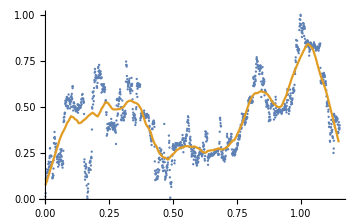

```mathematica
Show[ListPlot[#, ImageSize->Medium],   ListLinePlot[{{{0,0}},Table[{t, LoessR[#, Scaled[bestSpan], t ]}, {t, Min[#[[All, 1]]], Max[#[[All, 1]]], .005}]}]]&/@bubblesScaled
```

```mathematica
(* 1.b Detrend: *)
ℛs = Table[bubblesScaled[[i]][[All,2]]-bestFits[[i]], {i, bubbleN}];
```

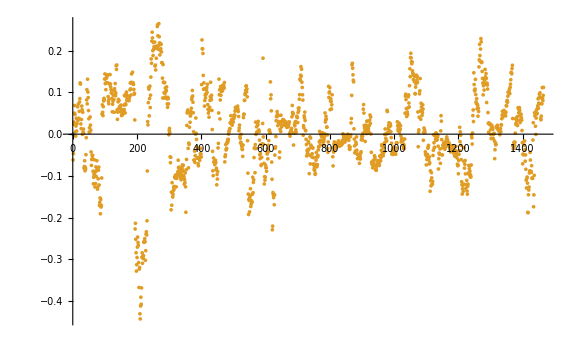

```mathematica
(* Plot residuals: *)
ListPlot[{{0,0},#}, ImageSize->Large]&/@ℛs
```

```mathematica
(* Standard deviations: *)
stdDevℛs=StandardDeviation /@ℛs
```

{0.0957221}

```mathematica
(* Standardized residuals: *)
stdℛs = MapThread[#1/#2&,{ℛs, stdDevℛs}];
```

```mathematica
(* RSS: *)
ℛsSS =Total[#^2]&/@ℛs
```

{13.4362}

```mathematica
(* Larger than in R: *)
MapThread[ToString[#1]<>" > "<>ToString[#2[[1]]]&,{ℛsSS,rErrors}]
```

{13.4362 > 8.06137}

```mathematica
(* Residual Standard Error(s): *)
ℛsSEs=MapThread[√(Total[#1^2]/(Length[#1]-#2[[1]]))&,{ℛs,rParams}]
```

{0.0963538}

```mathematica
(* Slightly larger than in R: *)
MapThread[ToString[#1]<>" > "<>ToString[#2[[2]]]&,{ℛsSEs,rErrors}]
```

{0.0963538 > 0.0748057}

```mathematica
(* Comparing formulas: *)
MapThread[√((#3[[1]])/(Length[#1]-#2[[1]]))&,{ℛs,rParams, rErrors}]
```

{0.0746337}

```mathematica
ℛsSEs=MapThread[√(Total[#1^2]/(#2[[2]]))&,{ℛs,rParams}]
```

{0.0965407}

```mathematica
(* Slightly larger than in R: *)
MapThread[ToString[#1]<>" > "<>ToString[#2[[2]]]&,{ℛsSEs,rErrors}]
```

{0.0965407 > 0.0748057}

```mathematica
(* Comparing formulas: *)
MapThread[√((#3[[1]])/(#2[[2]]))&,{ℛs,rParams, rErrors}]
```

{0.0747785}

```mathematica
(* 3. Fit LPPLS function: *)
tc=.
numParams=7;
lpplsModel=a +(tc-ti)^m(b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])
```

a+(tc-ti)^m (b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])

```mathematica
(* Select first bubble for fitting: *)
bubble=1
```

1

```mathematica
(* Use the selected bubble: *)
bubbleScaled=bubblesScaled[[bubble]];
```

```mathematica
(* Use the params for the selected bubble: *)
{estimatedNParams, effectiveDfs}=rParams[[bubble]]
```

{17.7681,1441.63}

```mathematica
(* Profiling over 0.1 < m < 1, 3 < ω < 14 and 1. < tc < 3 months in the future *)
minM=0.1;
maxM=1;
minω=3;
maxω=14;
months=3;
```

```mathematica
(* Try to estimate all the params using log-likelihood: *)
(* Define `months` in the future scaled interval endpoint: *)
bubbleScaled[[-1]][[1]]
maxTc=bubbleScaled[[-1]][[1]]+(bubblesDays[[bubble]]+30 months)/bubblesDays[[bubble]]//N
```

1.15366

3.62907

```mathematica
(* Define 3 days resolution scaled interval step: *)
stepTc=3/bubblesDays[[bubble]]//N
```

0.0491803

```mathematica
(* Define 3 days resolution scaled initial time step *)
stepTi=3/bubblesDays[[bubble]]//N
```

0.0491803

```mathematica
(* Slow. Shortcut below *)
Now[]
fits=Table[m=.;tc=.;
bestFit=MaximalBy[Flatten[ParallelTable[{tc,m,ω,nlm=NonlinearModelFit[Select[bubbleScaled,#[[1]]>= t1&],lpplsModel,{a,b,c,d}, ti];nlm["BestFitParameters"],
ℛ=nlm["FitResiduals"];
(* Fit an AR(1) process *)
ar1Process=ARProcess[μ,{ρ},σ^2];
estimatedAR1Model=FindProcessParameters[ℛ,ar1Process],
RSS=Total[ℛ^2],
RSS/(Length[ℛ]-numParams),
StandardDeviation[ℛ],
LogLikelihood[ar1Process/. estimatedAR1Model,ℛ]},{m,minM,maxM,1./10}, {ω,minω,maxω,1./10},  {tc, bubbleScaled[[-1]][[1]]+0.0001, maxTc,stepTc}],2], Last]//Flatten[#, 1]&;modelParams=Join[bestFit[[4]], {Subscript[T, 1]-> t1,tc-> bestFit[[1]],m-> bestFit[[2]], ω-> bestFit[[3]], RSS-> bestFit[[6]],ℛerror-> bestFit[[7]], ℛσ-> bestFit[[8]],LL-> bestFit[[9]]},bestFit[[5]]], {t1, Range[0,1/2+stepTi, stepTi]}]//AbsoluteTiming
```

Sat 24 Jan 2026 13:56:51GMT+1[]

{3249.66,{{a→1.01714,b→-0.372734,c→-0.116529,d→-0.0316236,T_1→0.,tc→2.23573,m→1.,ω→14.,RSS→24.987,ℛerror→0.0171378,ℛσ→0.130643,LL→3060.11,ρ→0.972538,σ→-0.0303958,μ→6.362×10^-18},{a→5.33542,b→-4.69108,c→-0.172487,d→-0.0476149,T_1→0.0491803,tc→2.23573,m→0.1,ω→14.,RSS→24.3593,ℛerror→0.0174618,ℛσ→0.13186,LL→2937.48,ρ→0.973651,σ→-0.0300592,μ→5.62432×10^-17},{a→1.19552,b→-0.733057,c→0.00173308,d→0.232857,T_1→0.0983607,tc→1.25212,m→0.1,ω→3.3,RSS→22.2606,ℛerror→0.0166996,ℛσ→0.128937,LL→2811.75,ρ→0.973152,σ→-0.0296657,μ→-1.35981×10^-17},{a→1.1501,b→-0.681899,c→0.00237085,d→0.237786,T_1→0.147541,tc→1.25212,m→0.1,ω→3.3,RSS→22.1192,ℛerror→0.0174167,ℛσ→0.131662,LL→2667.43,ρ→0.973787,σ→-0.0299363,μ→-2.50686×10^-20},{a→0.413165,b→0.222197,c→-0.0845284,d→0.40235,T_1→0.196721,tc→1.25212,m→0.4,ω→3.,RSS→15.172,ℛerror→0.0125596,ℛσ→0.111792,LL→2604.41,ρ→0.967207,σ→-0.0283826,μ→-2.41372×10^-18},{a→0.874983,b→-0.37165,c→0.00850154,d→0.266872,T_1→0.245902,tc→1.25212,m→0.1,ω→3.3,RSS→14.7876,ℛerror→0.0129149,ℛσ→0.113347,LL→2478.66,ρ→0.96821,σ→-0.0283401,μ→-8.59364×10^-18},{a→0.387018,b→0.310651,c→-0.0844931,d→0.478352,T_1→0.295082,tc→1.25212,m→0.5,ω→3.,RSS→13.6,ℛerror→0.0125577,ℛσ→0.111752,LL→2346.91,ρ→0.967816,σ→-0.0281106,μ→-2.93885×10^-18},{a→0.392168,b→0.255691,c→-0.0859769,d→0.414727,T_1→0.344262,tc→1.25212,m→0.4,ω→3.,RSS→12.6665,ℛerror→0.012406,ℛσ→0.111056,LL→2234.99,ρ→0.968803,σ→-0.0275097,μ→7.59247×10^-18},{a→0.863726,b→-0.372568,c→-0.0653069,d→0.25545,T_1→0.393443,tc→1.25212,m→0.1,ω→3.1,RSS→11.2348,ℛerror→0.0117274,ℛσ→0.107955,LL→2110.48,ρ→0.967183,σ→-0.0274152,μ→3.22187×10^-17},{a→0.751046,b→-0.252018,c→-0.0964052,d→0.251793,T_1→0.442623,tc→1.25212,m→0.1,ω→3.,RSS→10.158,ℛerror→0.0113371,ℛσ→0.106121,LL→1972.63,ρ→0.96571,σ→-0.0275363,μ→-5.2699×10^-19},{a→0.55344,b→-0.0169717,c→-0.0445028,d→0.271114,T_1→0.491803,tc→1.25212,m→0.1,ω→3.1,RSS→9.32985,ℛerror→0.0112003,ℛσ→0.105452,LL→1909.38,ρ→0.96919,σ→-0.0259591,μ→2.11346×10^-18},{a→0.752662,b→-0.228795,c→0.0211762,d→0.260845,T_1→0.540984,tc→1.25212,m→0.1,ω→3.3,RSS→9.25093,ℛerror→0.0119986,ℛσ→0.109114,LL→1769.44,ρ→0.973621,σ→-0.0248808,μ→4.00528×10^-18}}}

```mathematica
(* Shortcut: *)
fits=;
```

```mathematica
(* Timing in minutes: *)
fits[[1]]/60
```

54.1609

```mathematica
fits=fits[[2]];
```

```mathematica
fits[[All,{5,6,11,12}]]//TableForm
```

T_1→0. | tc→2.23573 | ℛσ→0.130643 | LL→3060.11
T_1→0.0491803 | tc→2.23573 | ℛσ→0.13186 | LL→2937.48
T_1→0.0983607 | tc→1.25212 | ℛσ→0.128937 | LL→2811.75
T_1→0.147541 | tc→1.25212 | ℛσ→0.131662 | LL→2667.43
T_1→0.196721 | tc→1.25212 | ℛσ→0.111792 | LL→2604.41
T_1→0.245902 | tc→1.25212 | ℛσ→0.113347 | LL→2478.66
T_1→0.295082 | tc→1.25212 | ℛσ→0.111752 | LL→2346.91
T_1→0.344262 | tc→1.25212 | ℛσ→0.111056 | LL→2234.99
T_1→0.393443 | tc→1.25212 | ℛσ→0.107955 | LL→2110.48
T_1→0.442623 | tc→1.25212 | ℛσ→0.106121 | LL→1972.63
T_1→0.491803 | tc→1.25212 | ℛσ→0.105452 | LL→1909.38
T_1→0.540984 | tc→1.25212 | ℛσ→0.109114 | LL→1769.44

```mathematica
(* Average tc: *)
meanTc=Total[fits[[All,6]][[All,2]]]/Length[fits]
```

1.41606

```mathematica
minTc=Min[fits[[All,6]][[All,2]]]
maxTc=Max[fits[[All,6]][[All,2]]]
```

1.25212

2.23573

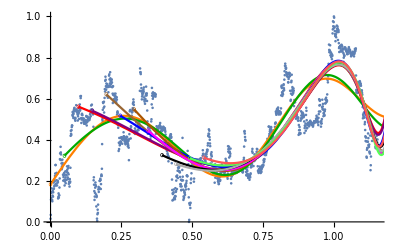

```mathematica
(* Plot of the results: *)
colors={Orange,Darker[Green],Red, Purple, Brown, Blue, Darker[Orange], Magenta,Black, Lighter[Gray], Lighter[Green], Lighter[Red], Lighter[Purple], Lighter[Brown], Lighter[Blue],Lighter[Orange]};
circles=Table[{colors[[Mod[i, Length[colors]]+1]],Thickness[0.0012],Circle[{i stepTi,lpplsModel/.fits[[i+1]]/.ti-> i stepTi},{0.005,0.0085}]}, {i, 0,Length[fits]-1}];
Show[ListPlot[bubbleScaled, ImageSize->Full, Epilog-> circles], Plot[Table[If[ti>i stepTi,Evaluate[lpplsModel/.fits[[i+1]]],""], {i,0,Length[fits]-1}], {ti, 0, maxTc}, PlotStyle->colors, Evaluated->True]]
```

```mathematica
(* 4. Rejection criteria: See if the residuals errors of the fits (ℛerror field) are below the 95% of the simulated (standardized) RSSs: *)
T1s=Subscript[T, 1]/.fits
ℛerrors=ℛerror/.fits
RSSs=RSS/.fits
ℛσs=ℛσ/.fits
```

{0.,0.0491803,0.0983607,0.147541,0.196721,0.245902,0.295082,0.344262,0.393443,0.442623,0.491803,0.540984}

{0.0171378,0.0174618,0.0166996,0.0174167,0.0125596,0.0129149,0.0125577,0.012406,0.0117274,0.0113371,0.0112003,0.0119986}

{24.987,24.3593,22.2606,22.1192,15.172,14.7876,13.6,12.6665,11.2348,10.158,9.32985,9.25093}

{0.130643,0.13186,0.128937,0.131662,0.111792,0.113347,0.111752,0.111056,0.107955,0.106121,0.105452,0.109114}

```mathematica
(* Only last bubble *)
npBestFit=bestFits[[bubble]];
```

```mathematica
nPℓ=Length[npBestFit];
nPℓ
```

1465

```mathematica
(* Plot of the residuals of the non-parametric fit vs the residuals of the parametric fit: *)
(* Non-parametric residuals: *)
npℛs=ℛs[[bubble]];
```

```mathematica
(* Parametric residuals: *)
fullFit[t_]:=lpplsModel/.fits[[1]]/.ti-> t
pℛs=Table[bubbleScaled[[i]][[2]]-fullFit[bubbleScaled[[i]][[1]]],{i,1,Length[bubbleScaled]}];
```

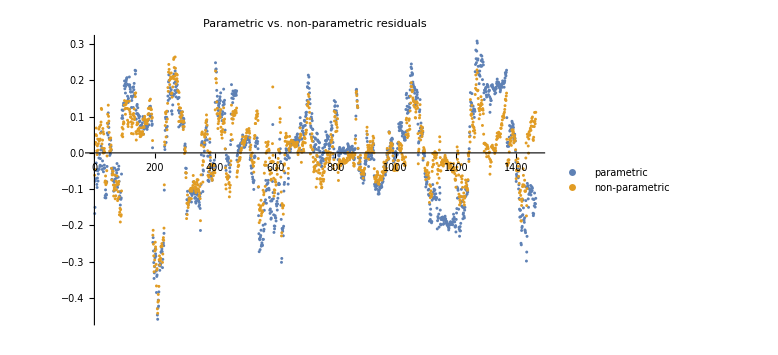

```mathematica
ListPlot[{pℛs,npℛs}, ImageSize->Large, {PlotLabel-> "Parametric vs. non-parametric residuals", PlotLegends->{"parametric","non-parametric"}}]
```

```mathematica
(* RSSs: *)
Total[#^2]&/@{npℛs, pℛs}
```

{13.4362,24.987}

```mathematica
(* Residual Standard Errors: *)
{√(Total[npℛs^2]/effectiveDfs),√(Total[pℛs^2]/(Length[pℛs]-numParams)) }
```

{0.0965407,0.130912}

```mathematica
(* Mean residual squared error: *)
{Total[npℛs^2]/effectiveDfs,Total[pℛs^2]/(Length[pℛs]-numParams) }
```

{0.00932011,0.0171378}

```mathematica
selN=Length[T1s];
selN
```

12

```mathematica
selNpBestFit=Table[npBestFit[[Floor[nPℓ T1s[[i]]+1];;]], {i,1,selN}];
```

```mathematica
Length/@selNpBestFit
```

{1465,1393,1321,1249,1177,1105,1033,961,889,817,745,673}

```mathematica
selBubbleScaled2=Table[bubbleScaled[[Floor[nPℓ T1s[[i]]+1];;]], {i,1,selN}];
```

```mathematica
Length/@selBubbleScaled2
```

{1465,1393,1321,1249,1177,1105,1033,961,889,817,745,673}

```mathematica
(* Export selected bubbles: *)
selBubbleScaledCsvs=MapIndexed[Export[base<>"csv/selBubbleScaled-"<>ToString[First[#2]]<>".tsv", Join[{{"time","value"}},#1]]&,selBubbleScaled2];
```

```mathematica
selBubbleScaled=#[[All,2]]&/@selBubbleScaled2;
```

```mathematica
selNpℛs=Table[selBubbleScaled[[i]]-selNpBestFit[[i]], {i, 1,selN}];
```

```mathematica
(* Structural checks: *)
Length/@selNpℛs
```

{1465,1393,1321,1249,1177,1105,1033,961,889,817,745,673}

```mathematica
selBubbleScaled[[1]][[1]]==bubbleScaled[[1]][[2]]
selNpBestFit[[1]][[1]]==npBestFit[[1]]
selNpℛs[[1]][[1]]==ℛs[[bubble]][[1]]
```

True

True

True

```mathematica
(* Magnitude of the parametric residual fits: *)
ℛerrors
```

{0.0171378,0.0174618,0.0166996,0.0174167,0.0125596,0.0129149,0.0125577,0.012406,0.0117274,0.0113371,0.0112003,0.0119986}

```mathematica
RSSs
```

{24.987,24.3593,22.2606,22.1192,15.172,14.7876,13.6,12.6665,11.2348,10.158,9.32985,9.25093}

```mathematica
(* For each selection, do the simulations, and compute all the statistics: *)
(* Standard deviations: *)
selStdDevℛs=StandardDeviation[#]& /@selNpℛs
```

{0.0957221,0.096999,0.0962378,0.0867857,0.0749321,0.0729069,0.0720354,0.0721493,0.0703243,0.0692018,0.0704094,0.0724784}

```mathematica
(* 1.c Fit AR(1) error model on the detrended data *)
(* Model the residuals with an AR(1) process *)
ar1Process=ARProcess[μ,{ρ},σ^2];
selEstimatedAR1Models=FindProcessParameters[#,ar1Process]&/@selNpℛs
```

{{ρ→0.950008,σ→-0.0298767,μ→0.000193531},{ρ→0.951644,σ→-0.0297876,μ→0.00019201},{ρ→0.951592,σ→-0.0295687,μ→0.0000919548},{ρ→0.938323,σ→-0.0299951,μ→0.000279875},{ρ→0.9261,σ→-0.0282582,μ→0.0000285519},{ρ→0.924175,σ→-0.0278355,μ→0.000338934},{ρ→0.924254,σ→-0.0274883,μ→0.00013542},{ρ→0.926489,σ→-0.0271372,μ→0.0000819911},{ρ→0.923687,σ→-0.0269295,μ→0.000210098},{ρ→0.935126,σ→-0.0245043,μ→0.000370007},{ρ→0.934612,σ→-0.0250257,μ→0.000145299},{ρ→0.936259,σ→-0.0254435,μ→0.000332398}}

```mathematica
(* Compute the log-likelihood of the fit *)
selEstimatedProcesses=ar1Process/.#&/@selEstimatedAR1Models
logLikelihoods=Table[LogLikelihood[selEstimatedProcesses[[i]],selNpℛs[[i]]], {i, Length[T1s]}]
```

{ARProcess[0.000193531,{0.950008},0.000892619],ARProcess[0.00019201,{0.951644},0.000887303],ARProcess[0.0000919548,{0.951592},0.00087431],ARProcess[0.000279875,{0.938323},0.000899707],ARProcess[0.0000285519,{0.9261},0.000798528],ARProcess[0.000338934,{0.924175},0.000774816],ARProcess[0.00013542,{0.924254},0.000755605],ARProcess[0.0000819911,{0.926489},0.00073643],ARProcess[0.000210098,{0.923687},0.000725197],ARProcess[0.000370007,{0.935126},0.00060046],ARProcess[0.000145299,{0.934612},0.000626283],ARProcess[0.000332398,{0.936259},0.000647371]}

{3071.32,2928.4,2784.03,2660.47,2537.44,2395.35,2254.46,2110.48,1958.41,1878.5,1698.65,1523.59}

```mathematica
(* Step 2: Characterize error variance. *)
(* 2.a Bootstrap the residuals from step 1 and feed them through the fitted AR(1) to simulate errors. *)
selNPointss=Length/@selNpℛs;
nSims=1000;
selSims=ParallelTable[RandomFunction[selEstimatedProcesses[[i]],{0,selNPointss[[i]]-1},nSims], {i,selN}];
selNpℛsPlots=ParallelTable[MapThread[{#1,#2}&,{Range[0,selNPointss[[i]]-1],selNpℛs[[i]][[;;selNPointss[[i]]]]}], {i,selN}];
selPaths=#["Paths"]&/@selSims;
```

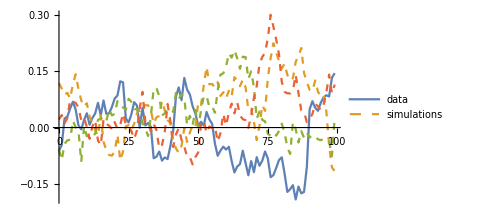
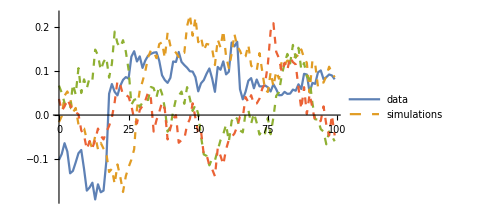
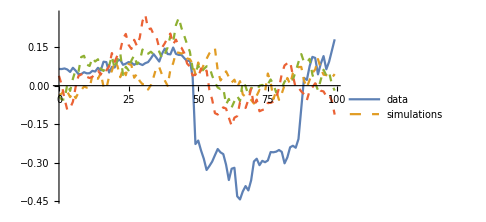
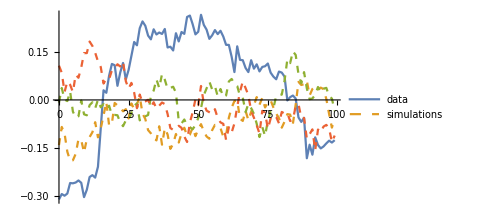
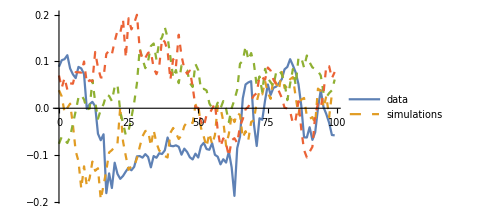
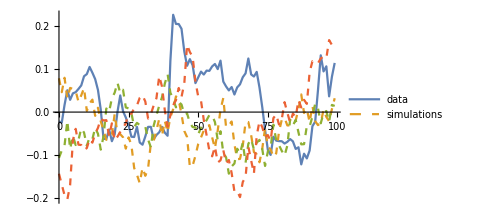
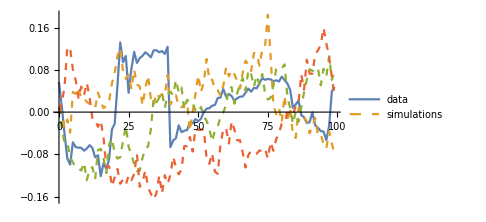
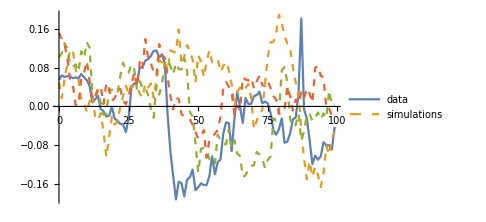

```mathematica
(* Show some simulations and data points *)
showSims=3;
showPoints=100;
Table[ListLinePlot[Join[{selNpℛsPlots[[i]][[;;showPoints]]}, selPaths[[i]][[;;showSims,;;showPoints]]],PlotStyle->{Thick, Dashed, Dashed, Dashed},PlotLegends->{"data","simulations"}, ImageSize->Medium],{i,selN}]
```

```mathematica
(* The estimated number of parameters of the sample selections fits: *)
(* From R's loess, using list of (selections) effective dfs: *)
selRInputs="bestSpan <- "<> ToString[bestSpan]<>"\n"<>
"bubbleScaled<-read.csv(\""<>ToString[#]<>"\", sep='\\t', header=TRUE)"<>"\n"<>
"bubble.lo<-loess(value~time, bubbleScaled, degree=1, span=bestSpan)"<>"\n"<>
"pred=predict(bubble.lo, 1, se=TRUE);"<>"\n"<>
"bubble.lo$enp"<>"\n"<>
"pred$df"<>"\n"<>
"sum(bubble.lo$residuals^2)"<>"\n"<>
"bubble.lo$s"<>"\n"<>
"pred$se.fit"&/@selBubbleScaledCsvs;
```

```mathematica
selRRuns=RunProcess[{"/usr/local/bin/R", "--vanilla"}, All, #]&/@selRInputs;
```

```mathematica
(* {Estimated number of params, Degrees of freedom}: *)
selRParams=ToExpression[StringSplit[#][[2]]]&/@StringSplit[#["StandardOutput"], "\n"][[-10;;-8;;2]]&/@selRRuns
```

{{17.7681,1441.63},{17.7095,1369.71},{17.6567,1297.78},{17.5858,1225.87},{17.8468,1153.53},{17.7768,1081.63},{17.7127,1009.71},{17.6233,937.83},{17.5286,865.955},{17.8917,793.482},{17.7959,721.609},{17.6974,649.74}}

```mathematica
effectiveDfs
estimatedNParams
(*selEstimatedDfs=Table[Length[selBubbleScaled[[i]]]-estimatedNParams, {i, selN}]*)
selEffectiveDfs=Table[selRParams[[i]][[2]], {i, selN}]
```

1441.63

17.7681

{1441.63,1369.71,1297.78,1225.87,1153.53,1081.63,1009.71,937.83,865.955,793.482,721.609,649.74}

```mathematica
(* The "mean" RSSs (RSS/df) of the simulations: *)
selMeanRSSs=Table[Map[Total[(#[[All,2]])^2]/selEffectiveDfs[[i]]&,selPaths[[i]]], {i, selN}];
(*Histogram[#, ImageSize->Medium]&/@selMeanRSSs*)
```

```mathematica
memory:=Row[{"Memory Used: ",MemoryInUse[]/1024^3.," GB"}];
Needs["Utilities`CleanSlate`"]
memory
```

Memory Used: 1.48688 GB

```mathematica
Remove[selSims]
Remove[selNpℛsPlots]
memory
```

Memory Used: 1.48697 GB

```mathematica
CleanSlate[];
memory
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 204897 Kb

Memory Used: 1.29169 GB

```mathematica
(* The standardized "mean" RSSs: *)
selStdMeanRSSs=Table[Map[#/selStdDevℛs[[i]]&,selMeanRSSs[[i]]], {i, selN}];
(*Histogram[#, ImageSize->Medium]&/@selStdMeanRSSs*)
```

```mathematica
(* Count *)
selCounts=Table[With[{ℛerror= ℛerrors[[i]]},Select[selMeanRSSs[[i]],#>ℛerror &]//Length],{i,selN}]
```

{1,0,0,0,0,0,0,0,0,0,0,1}

```mathematica
selPValues=Table[selCounts[[i]]/Length[selMeanRSSs[[i]]], {i, selN}]//N
```

{0.001,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.001}

```mathematica
selRejected=#<(1-0.95)&/@selPValues
```

{True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
(* Take the first / largest interval that is not rejected *)
firstNotRejectedIndex=Select[Table[{i,selRejected[[i]]==False},{i,selN}], #[[2]]&]//First//#[[1]]&
```

First::nofirst: {} has zero length and no first element.

{}

```mathematica
(* As a fallback (if all rejected), take the one with the highest non-zero p-value *)
highestPRejected=ReverseSortBy[Select[MapIndexed[{#1, #2[[1]]}&, selPValues], 0< #[[1]]<(1-0.95)&], {#[[1]],-#[[2]]}&];
highestPRejectedIndex=If[Length[highestPRejected]>0, First[highestPRejected][[2]],{}]
```

1

```mathematica
(* As a fallback (if all rejected, and no positive p-values), take the one with the min tc *)
minTc=Min[fits[[;;,6,2]]]
minTcIndex=Select[Table[{i,fits[[i,6,2]]==minTc},{i,selN}],#[[2]]&]//First//#[[1]]&
```

1.25212

3

```mathematica
index=If[NumericQ[firstNotRejectedIndex], firstNotRejectedIndex,If[NumericQ[highestPRejectedIndex], highestPRejectedIndex, minTcIndex]]
```

1

```mathematica
selFit={fits[[index]], "index"-> index}//Flatten
```

{a→1.01714,b→-0.372734,c→-0.116529,d→-0.0316236,T_1→0.,tc→2.23573,m→1.,ω→14.,RSS→24.987,ℛerror→0.0171378,ℛσ→0.130643,LL→3060.11,ρ→0.972538,σ→-0.0303958,μ→6.362×10^-18,index→1}

```mathematica
bestIndex=index
fit=fits[[bestIndex]]
```

1

{a→1.01714,b→-0.372734,c→-0.116529,d→-0.0316236,T_1→0.,tc→2.23573,m→1.,ω→14.,RSS→24.987,ℛerror→0.0171378,ℛσ→0.130643,LL→3060.11,ρ→0.972538,σ→-0.0303958,μ→6.362×10^-18}

```mathematica
(* Estimate tc 95% CI by Profile Likelihood *)
m=.
ω=.
tc=.
```

```mathematica
(* Do it over the best params *)
bestm=m/.fit
bestω=ω/.fit
bestTc=tc/.fit
bestLL=LL/.fit
```

1.

14.

2.23573

3060.11

```mathematica
t1=Subscript[T, 1]/.fit
```

0.

```mathematica
(* Selected best bubble: *)
bubbleBest=Select[bubbleScaled, #[[1]]>= t1&];
```

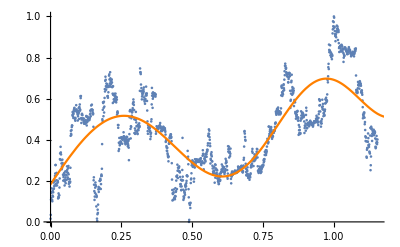

```mathematica
(* Best fit plot *)
Show[ListPlot[bubbleBest, ImageSize->Full], Plot[Evaluate[lpplsModel/.fit], {ti, t1, bestTc}, PlotStyle->{colors[[bestIndex]]}, Evaluated->True]]
```

```mathematica
(* Profile-likelihood-based 95% C.I. for Subscript[t, c]: *)
(* Get nlm function: *)
lpplsModel
```

a+(tc-ti)^m (b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])

```mathematica
(* Parametrize it: *)
fit
```

{a→1.01714,b→-0.372734,c→-0.116529,d→-0.0316236,T_1→0.,tc→2.23573,m→1.,ω→14.,RSS→24.987,ℛerror→0.0171378,ℛσ→0.130643,LL→3060.11,ρ→0.972538,σ→-0.0303958,μ→6.362×10^-18}

```mathematica
bestLppls[x_, testTc_:bestTc]:= lpplsModel/.fit[[1;;4]]/.fit[[7;;8]]/.ti-> x/.tc-> testTc
```

```mathematica
mlℛ = Map[#[[2]]-bestLppls[#[[1]]]&, bubbleBest];
```

```mathematica
(* Fit an AR(1) process (Perhaps re-utilize / recompute the non-parametric residuals model, fitted over the selected interval): *)
ar1Process=ARProcess[μ,{ρ},σ^2];
estimatedAR1Model=FindProcessParameters[mlℛ,ar1Process]
```

{ρ→0.972538,σ→-0.0303958,μ→6.362×10^-18}

```mathematica
bestLL==LogLikelihood[ar1Process/. estimatedAR1Model,mlℛ]
```

True

```mathematica
(* They match. *)
```

```mathematica
(* Now sligthly vary tc, and recompute residuals until the LL is 1.92 times below the max: *)
lowCItc=bestTc;
lowCILL=bestLL;
```

```mathematica
target=1.92;
epsilon=1/10000;
precision=1/1000;
oldSign=1;
Monitor[While[delta=bestLL-lowCILL;Not[target<=delta <target+epsilon],
sign=Sign[delta-target];
lowCItc=lowCItc+ precision sign;
ℛ = Map[#[[2]]-bestLppls[#[[1]], lowCItc]&, bubbleBest];
lowCILL=LogLikelihood[ar1Process/. estimatedAR1Model,ℛ];
precision=If[sign!=oldSign,precision /2,precision];
oldSign=sign;
],{delta}]
delta
{lowCItc, bestTc}
```

1.92006

{2.19952,2.23573}

```mathematica
(* Let's do the upper leg of the CI: *)
highCItc=bestTc;
highCILL=bestLL;
```

```mathematica
target=1.92;
epsilon=1/10000;
precision=1/100;
oldSign=-1;
Monitor[While[delta=bestLL-highCILL;Not[target<=delta <target+epsilon],
sign=Sign[delta-target];
highCItc=highCItc- precision sign;
ℛ = Map[#[[2]]-bestLppls[#[[1]], highCItc]&, bubbleBest];
highCILL=LogLikelihood[ar1Process/. estimatedAR1Model,ℛ];
precision=If[sign!=oldSign,precision /2,precision];
oldSign=sign;
],delta]
delta
{lowCItc, bestTc, highCItc}
```

1.92007

{2.19952,2.23573,2.28331}

```mathematica
(* Dates correction: *)
lastScaledTc=bubbleBest[[-1]][[1]]
```

1.15366

```mathematica
(* Now compute the equivalent date of the low CI tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] lowCItc/lastScaledTc]
```

Thu 19 Mar 2026 07:11:16

```mathematica
(* And the best tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] bestTc/lastScaledTc]
```

Sat 21 Mar 2026 05:08:35

```mathematica
(* And the equivalent date of the high CI tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] highCItc/lastScaledTc]
```

Mon 23 Mar 2026 17:31:00

```mathematica
(* With the mean tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] meanTc/lastScaledTc]
```

Thu 5 Feb 2026 20:58:45

```mathematica
(* With the max tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] maxTc/lastScaledTc]
```

Sat 21 Mar 2026 05:08:35

```mathematica
(* With the min tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] minTc/lastScaledTc]
```

Wed 28 Jan 2026 04:56:47

```mathematica
(* For reference: *)
{#[[5]],DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] #[[5]][[2]]/lastScaledTc],#[[6]],DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] #[[6]][[2]]/lastScaledTc]}&/@fits//TableForm
```

T_1→0. | Sun 23 Nov 2025 00:00:00 | tc→2.23573 | Sat 21 Mar 2026 05:08:35
T_1→0.0491803 | Tue 25 Nov 2025 14:24:35 | tc→2.23573 | Sat 21 Mar 2026 05:08:35
T_1→0.0983607 | Fri 28 Nov 2025 04:49:10 | tc→1.25212 | Wed 28 Jan 2026 04:56:47
T_1→0.147541 | Sun 30 Nov 2025 19:13:46 | tc→1.25212 | Wed 28 Jan 2026 04:56:47
T_1→0.196721 | Wed 3 Dec 2025 09:38:21 | tc→1.25212 | Wed 28 Jan 2026 04:56:47
T_1→0.245902 | Sat 6 Dec 2025 00:02:57 | tc→1.25212 | Wed 28 Jan 2026 04:56:47
T_1→0.295082 | Mon 8 Dec 2025 14:27:32 | tc→1.25212 | Wed 28 Jan 2026 04:56:47
T_1→0.344262 | Thu 11 Dec 2025 04:52:07 | tc→1.25212 | Wed 28 Jan 2026 04:56:47
T_1→0.393443 | Sat 13 Dec 2025 19:16:43 | tc→1.25212 | Wed 28 Jan 2026 04:56:47
T_1→0.442623 | Tue 16 Dec 2025 09:41:18 | tc→1.25212 | Wed 28 Jan 2026 04:56:47
T_1→0.491803 | Fri 19 Dec 2025 00:05:54 | tc→1.25212 | Wed 28 Jan 2026 04:56:47
T_1→0.540984 | Sun 21 Dec 2025 14:30:29 | tc→1.25212 | Wed 28 Jan 2026 04:56:47

```mathematica
(* Compute market cap at the low leg of the best Tc: *)
bestM=bestLppls[bestTc-epsilon,bestTc]
```

1.01711

```mathematica
lowCIM=bestLppls[lowCItc,bestTc]
```

1.00766

```mathematica
lastScaledM=bubbleBest[[-1]][[2]]
Exp[lastScaledM]
```

0.4011

1.49347

```mathematica
lastPriceDate
```

2026-01-23

```mathematica
(* Closing market cap at lastPriceDate date (`$lastPriceDate`) (https://coinmarketcap.com/currencies/bitcoin/historical-data/https://coinmarketcap.com/currencies/bitcoin/historical-data/Nonehttps://coinmarketcap.com/currencies/bitcoin/historical-data/HyperlinkActionRecycledHyperlinkActive) (Millions of USD): *)
(* Automated download *)
timeStartTs=UnixTime[lastPriceDate];
timeEndTs=timeStartTs+86400;
latestMarketCapUrl="https://api.coinmarketcap.com/data-api/v3.1/cryptocurrency/historical?id=1&convertId=2781&timeStart="<>ToString[timeStartTs]<>"&timeEnd="<>ToString[timeEndTs]<>"&interval=1d"
```

https://api.coinmarketcap.com/data-api/v3.1/cryptocurrency/historical?id=1&convertId=2781&timeStart=1769122800&timeEnd=1769209200&interval=1d

```mathematica
latestMarketCapData=Import[latestMarketCapUrl]
```

```mathematica
latestMarketCapInner=Flatten[latestMarketCapData[[1]][[2]][[5]][[2]]]
```

```mathematica
(* Build a list of timeCloses and marketCaps: *)
latestMarketCapWithTime=SortBy[MapThread[{#1, #2[[2]][[7]]}&,{latestMarketCapInner[[2;;-1;;5]], latestMarketCapInner[[5;;-1;;5]]}], First];
```

```mathematica
latestMarketCap=latestMarketCapWithTime[[-1]][[2]][[2]]/10^7
```

178832.360467052

```mathematica
(* Plot predicted market cap evolution (USD) :*)
fixDate[brokenDate_]:= StringTake[brokenDate,2]<>"/"<>StringTake[brokenDate,3;;]
ticksH[min_,max_]:=Table[{i,Rotate[fixDate[Block[{$DateStringFormat={"Day","Month","/","YearShort"}},DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]]i/lastScaledTc]]], π/3]},{i,{t1,lastScaledTc,lowCItc, bestTc, highCItc}}]
```

```mathematica
ticksVM[min_,max_]:=Table[{i,"$ "<>ToString[IntegerPart[i latestMarketCap/Exp[lastScaledM]]]<>"M"},{i,min, max,100}]
```

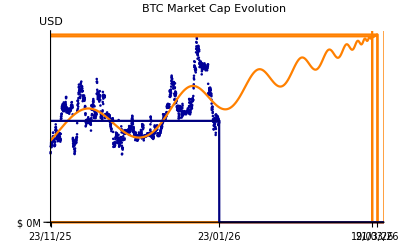

```mathematica
marketCapPrediction=Show[ListPlot[{#[[1]], Exp[#[[2]]]}&/@bubbleBest, {ImageSize->Full,PlotLabel->"BTC Market Cap Evolution",PlotRange->{{0,maxTc},{0,Exp[bestM]}}, Ticks->{ticksH,ticksVM},PlotStyle->Darker[Blue, .4], TicksStyle->Directive["Label", 10],AxesLabel->"USD"}], Plot[{Evaluate[Exp[lpplsModel/.fit]],UnitStep[ti-lowCItc]Exp[bestM+1],UnitStep[ti-highCItc]Exp[bestM+1]/.fit, UnitStep[lowCItc-ti]Exp[lowCIM],UnitStep[bestTc-ti]Exp[bestM],UnitStep[lastScaledTc-ti]Exp[lastScaledM]}, {ti, 0, maxTc+1/10}, {PlotStyle->{colors[[bestIndex]],Orange, Orange, Orange, colors[[bestIndex]], Darker[Blue, .5]}}]]
```

```mathematica
Export[base <>"png/BTC_MarketCapPrediction-"<>lastPriceDate<>".png",marketCapPrediction]
```

/Users/mauro/Projects/Bitcoin/png/BTC_MarketCapPrediction-2026-01-23.png

```mathematica
mToMarketCap[m_]:= latestMarketCap/Exp[lastScaledM] Exp[m]
```

```mathematica
lowCIMarketCap=mToMarketCap[lowCIM]
```

327999.

```mathematica
bestMarketCap=mToMarketCap[bestM]
```

331113.

```mathematica
(* The price is the ratio of the market cap (in Millions USD) to the (predicted) supply at the date: *)
mToPrice[m_, date_]:=mToMarketCap[m]10^7/supplyFunction[UnixTime[date]]
```

```mathematica
tcToDate[tc_]:= DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]]tc/lastScaledTc]
tcToDate[lastScaledTc]
```

Fri 23 Jan 2026 00:00:00

```mathematica
(* Check: *)
lastPrice=mToPrice[lastScaledM,tcToDate[lastScaledTc]]
```

89508.4

```mathematica
lowCIPrice=mToPrice[lowCIM, tcToDate[lowCItc]]//N
```

163975.

```mathematica
bestPrice=mToPrice[bestM, tcToDate[bestTc]]
```

165525.

```mathematica
(* Plot predicted price evolution (USD) :*)
ticksVPrice[min_,max_]:=Table[{i,"$"<>ToString[IntegerPart[i/1000]]<>"K"},{i,min, max,IntegerPart[max/100000]10000}]
```

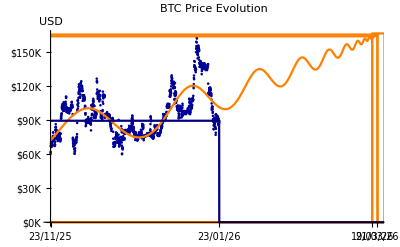

```mathematica
pricePrediction=Show[ListPlot[{#[[1]], mToPrice[#[[2]], tcToDate[#[[1]]]]}&/@bubbleBest, {ImageSize->Full,PlotLabel->"BTC Price Evolution",PlotRange->{{0,maxTc},{0,bestPrice}}, Ticks->{ticksH,ticksVPrice},PlotStyle->Darker[Blue, .4], TicksStyle->Directive["Label", 10],AxesLabel->"USD"}], Plot[{Evaluate[mToPrice[lpplsModel/.fit, tcToDate[ti]]],UnitStep[ti-lowCItc](bestPrice+1000),UnitStep[ti-highCItc](bestPrice+1000)/.fit, UnitStep[lowCItc-ti]lowCIPrice,UnitStep[bestTc-ti]bestPrice,UnitStep[lastScaledTc-ti]lastPrice}, {ti, 0, maxTc+1/10}, {PlotStyle->{colors[[bestIndex]],Orange, Orange, Orange, colors[[bestIndex]], Darker[Blue, .5]}}]]
```

```mathematica
Export[base <>"png/BTC_PricePrediction-"<>lastPriceDate<>".png",pricePrediction]
```

/Users/mauro/Projects/Bitcoin/png/BTC_PricePrediction-2026-01-23.png